# BZ State Space and Novel Cellular Automata Rules

#### Abhishek Sharma Cronin Lab University of Glasgow abhishek.sharma@glasgow.ac.uk

```mathematica
baseDirectory=NotebookDirectory[]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/

## State Space Description for Classical Cellular Automata

In this section, we start with description of the state space on one-dimensional elementary cellular automata rules. Consider a cellular automata space consisting of n cells, hence for a two state cellular automata, total number of global possible states are 2^n. We start with considering a complete graph of all possible combinations for a given cell size, and using Jaccard index / dissimilarity for two given Boolean sequences, we create a graph with connectivity based on Jaccard index.

```mathematica
nCells=4; (* Total number of cells *)
```

```mathematica
globalStates=Tuples[{0,1},nCells]; (* Total Number of Global States *)
```

```mathematica
stateList=Range@Length@globalStates;
```

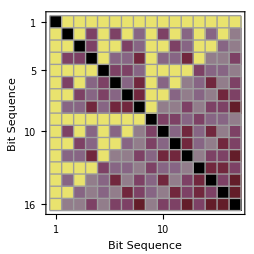

```mathematica
MatrixPlot[Partition[JaccardDissimilarity[#⟦1⟧,#⟦2⟧]&/@Tuples[{globalStates,globalStates}],Length@globalStates],ColorFunction->"PlumColors",ColorFunctionScaling->False,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},FrameLabel->{"Bit Sequence","Bit Sequence"},Mesh-> All]
```

Plotting with a circular and spiral embedding.

```mathematica
p1 = HighlightGraph[Graph[#⟦1⟧<->#⟦2⟧&/@Tuples[{Range[Length@globalStates],Range[Length@globalStates]}],VertexLabels->Placed[Automatic,Center],VertexSize->0.4,EdgeStyle->Thin,GraphLayout->"CircularEmbedding"],Flatten@Table[Style[i<->j,ColorData["Rainbow"][1-JaccardDissimilarity[globalStates⟦i⟧,globalStates⟦j⟧]]],{i,Length@globalStates},{j,Length@globalStates}]];
```

```mathematica
p2=HighlightGraph[Graph[#⟦1⟧<->#⟦2⟧&/@Tuples[{Range[Length@globalStates],Range[Length@globalStates]}],VertexLabels->Placed[Automatic,Center],VertexSize->1.0,EdgeStyle->Thin,GraphLayout->"SpiralEmbedding"],Flatten@Table[Style[i<->j,ColorData["Rainbow"][1-JaccardDissimilarity[globalStates⟦i⟧,globalStates⟦j⟧]]],{i,Length@globalStates},{j,Length@globalStates}]];
```

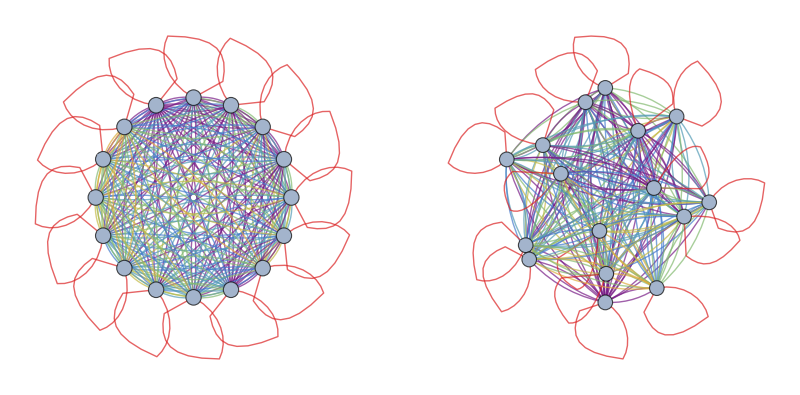

```mathematica
GraphicsRow[{p1,p2}]
```

```mathematica
Export[baseDirectory<>"StateNetwork_Circular.svg",p1]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/StateNetwork_Circular.svg

```mathematica
Export[baseDirectory<>"StateNetwork_Circular.png",p1,ImageResolution-> 300]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/StateNetwork_Circular.png

```mathematica
Export[baseDirectory<>"StateNetwork_Spiral.svg",p2]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/StateNetwork_Spiral.svg

```mathematica
Export[baseDirectory<>"StateNetwork_Spiral.png",p2,ImageResolution->300]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/StateNetwork_Spiral.png

Looking at the connectivity map for higher number of cells by estimating Jaccard dissimilarity index.

```mathematica
nCells=12; (* Total number of cells *)
globalStates=Tuples[{0,1},nCells]; (* Total Number of Global States *)
stateList=Range@Length@globalStates; (* Defining state list using single numbers forp plotting *)
p3=MatrixPlot[Partition[JaccardDissimilarity[#⟦1⟧,#⟦2⟧]&/@Tuples[{globalStates,globalStates}],Length@globalStates],ColorFunction->"PlumColors",ColorFunctionScaling->False,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},FrameLabel->{"Bit Sequence","Bit Sequence"}]
```

-Graphics-

```mathematica
Export[baseDirectory<>"StateNetwork_MatrixPlot.svg",p3,ImageResolution-> 300]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/StateNetwork_MatrixPlot.svg

## State Space Exploration by Elementary Cellular Automata Rules

We start with elementary cellular automata rule 30 : whose rule plot looks like :

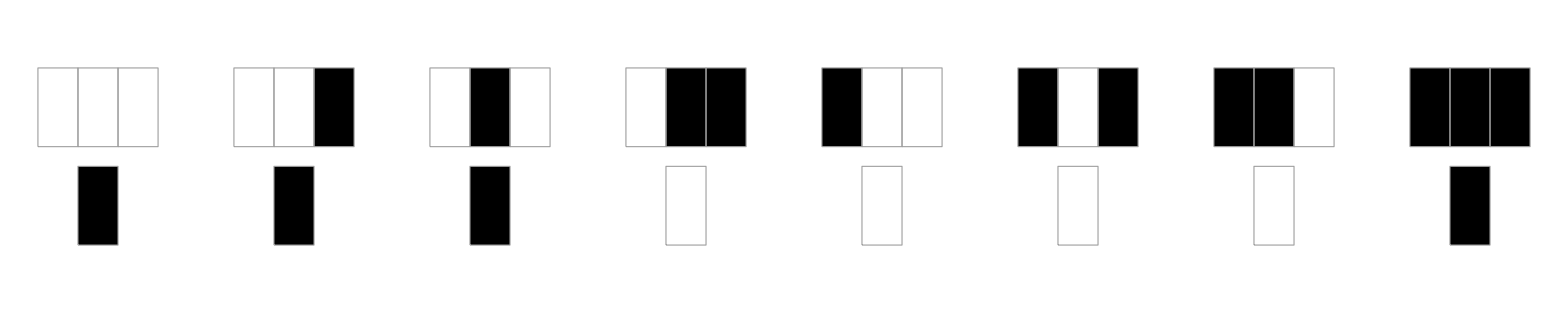

```mathematica
CARule=RulePlot[CellularAutomaton[{30,2}],ColorRules->{0-> Black,1->White}]
```

```mathematica
CAEvolution=ArrayPlot[CellularAutomaton[30,{{1},0},100],ImageSize->Medium]
```

-Graphics-

```mathematica
calJaccardSim[rule_,steps_]:= Block[{CAStates},CAStates=CellularAutomaton[rule,{{1},0},steps];JaccardDissimilarity[#⟦1⟧,#⟦2⟧]&/@Table[{CAStates⟦i⟧,CAStates⟦i+1⟧},{i,Length@CAStates-1}]]
```

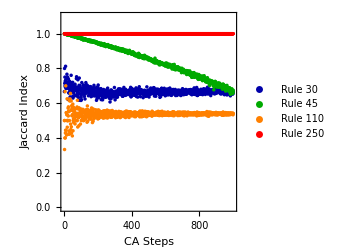

```mathematica
dissimilarityCA=ListPlot[{calJaccardSim[30,10^3],calJaccardSim[45,10^3],calJaccardSim[110,10^3],calJaccardSim[250,10^3]},PlotRange-> {0,1.1},Frame-> True,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{{Darker@Blue,PointSize[0.01]},{Darker@Green,PointSize[0.01]},{Orange,PointSize[0.01]},{Red,PointSize[0.01]}},FrameLabel->{"CA Steps","Jaccard Index"},AspectRatio->1,PlotLegends-> Placed[LineLegend[{"Rule 30","Rule 45","Rule 110","Rule 250"},Spacings-> 0.25],{0.75,0.23}],ImageSize->250]
```

```mathematica
Export[baseDirectory<>"Rule30.svg",CARule]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/Rule30.svg

```mathematica
Export[baseDirectory<>"Rule30.png",CARule,ImageResolution-> 300]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/Rule30.png

```mathematica
Export[baseDirectory<>"CA_Rule30.svg",CAEvolution]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/CA_Rule30.svg

```mathematica
Export[baseDirectory<>"CA_Rule30.png",CAEvolution,ImageResolution-> 300]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/CA_Rule30.png

```mathematica
Export[baseDirectory<>"Jaccard_Dissim.svg",dissimilarityCA,ImageResolution-> 300]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/Jaccard_Dissim.svg

```mathematica
Export[baseDirectory<>"Jaccard_Dissim.png",dissimilarityCA]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/Jaccard_Dissim.png

## BZ Cellular Automata State Space

To quantify the BZ experimental space, we start with quantifying the total number of possible global states. For k possible discrete chemical states and n×n grid and p possible cell stirrer states and q interfacial states, the total global states are given by

```mathematica
globalChemStates[k_,n_]:=k^(n n)
```

```mathematica
globalInputStates[p_,q_,n_]:=p^(n n)q^(2n(n-1))
```

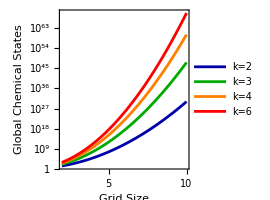

```mathematica
plot1=LogPlot[Evaluate@{globalChemStates[#,n]&/@{2,3,4,5}},{n,2,10},PlotRange-> Full,Frame-> True,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{{Darker@Blue,PointSize[0.01]},{Darker@Green,PointSize[0.01]},{Orange,PointSize[0.01]},{Red,PointSize[0.01]}},FrameLabel->{"Grid Size","Global Chemical States"},AspectRatio->1,PlotLegends-> Placed[LineLegend[{"k=2","k=3","k=4","k=6"},Spacings-> 0.25],{0.20,0.75}],ImageSize->200]
```

```mathematica
Export[baseDirectory<>"ChemicalStates.svg",plot1]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/ChemicalStates.svg

```mathematica
Export[baseDirectory<>"ChemicalStates.png",plot1,ImageResolution-> 300]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/ChemicalStates.png

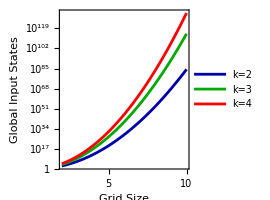

```mathematica
plot2=LogPlot[Evaluate@{globalInputStates[#,2,n]&/@{2,4,6}},{n,2,10},PlotRange-> Full,Frame-> True,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->{{Darker@Blue,PointSize[0.01]},{Darker@Green,PointSize[0.01]},{Red,PointSize[0.01]},{Red,PointSize[0.01]}},FrameLabel->{"Grid Size","Global Input States"},AspectRatio->1,PlotLegends-> Placed[LineLegend[{"k=2","k=3","k=4","k=6"},Spacings-> 0.25],{0.20,0.75}],ImageSize->200]
```

```mathematica
Export[baseDirectory<>"InputStates.svg",plot2]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/InputStates.svg

```mathematica
Export[baseDirectory<>"InputStates.png",plot2,ImageResolution->300]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/InputStates.png

Creating BZ Cellular Automata rules : One dimensional BZ-CA can be variable depending on the physical model we consider. Due to complex hydrodynamic phenomena, in this section we only consider simple rules where both state machines can be defined precisely.

## One dimensional BZ-CA and 2 PWM states : Type 1

In this section, we describe one dimensional Cellular Automata based on chemical states defined by BZ oscillations and controlled by PWM states of the cell and the interfacial stirrers. To simulate the evolution of the cellular automata, we consider two different state machines :
	→ state_rule : defines the PWM levels to be applied based on the current cellular automata state
	→ phen_rule : simple rules based on the phenomenological model to describe the effect of PWM states of the stirrers on the evolving chemical states.

In this BZ-CA model, the PWM states are updated based on the current discrete chemical states. And, the new chemical states depends only on the applied PWM levels NOT on the previous chemical states. So, the coupling between the two chemical states is based on the applied PWM levels. In the next section, we will consider the more complex case in which  the new chemical states depends not only on the PWM levels of a given cell and its neighbours, but also on the previous chemical states (strong hysteresis).

```mathematica
nCells=100;(* Number of cells *)
```

```mathematica
nPWMCell=2; (* Number of discrete PWM levels of cell strirrers *)
```

```mathematica
nPWMIntf=2;(* Number of discrete PWM levels of interfacial strirrers *)
```

```mathematica
nChemSt=2;(* Number of discrete chemical states derived from BZ oscillation patterns with chemical clocking *)
```

Assuming a simple rule, where the next state depends only on the nearest neighbours,
	
	CS_i^t=f(C_i^t, C_(i-1)^t, C_(i+1)^t) 
	C_i^(t+1)= g(CS_i^t, CS_(i-1)^t, CS_(i+1)^t,CI_(i, i+1)^t,CI_(i, i-1)^t)
	
Two Cell PWM States rule table: Total possible cases is 32, however they can be substantially reduced. 

	{CS_i^t==1, CS_(i-1)^t==1/0,CS_(i+1)^t==1/0, CI_(i, i+1)^t==1/0, CI_(i, i-1)^t==1/0}, C_i^(t+1)→𝒫(1)= 1  
	{CS_i^t==0, CS_(i-1)^t==0,CS_(i+1)^t==0, CI_(i, i+1)^t==1/0, CI_(i, i-1)^t==1/0}, C_i^(t+1)→𝒫(1)= 0   
	{CS_i^t==0, CS_(i-1)^t==1/0,CS_(i+1)^t==1/0, CI_(i, i+1)^t==0, CI_(i, i-1)^t==0}, C_i^(t+1)→𝒫(1)= 0  
	{CS_i^t==0, CS_(i-1)^t==1,CS_(i+1)^t==1, CI_(i, i+1)^t==1, CI_(i, i-1)^t==1}, C_i^(t+1)→𝒫(1)= 0.8  
	{CS_i^t==0, CS_(i-1)^t==1,CS_(i+1)^t==1/0, CI_(i, i+1)^t==0, CI_(i, i-1)^t==1}, C_i^(t+1)→𝒫(1)= 0.5   
	{CS_i^t==0, CS_(i-1)^t==1/0,CS_(i+1)^t==1, CI_(i, i+1)^t==1, CI_(i, i-1)^t==0}, C_i^(t+1)→𝒫(1)= 0.5   
	{CS_i^t==0, CS_(i-1)^t==1,CS_(i+1)^t==0, CI_(i, i+1)^t==1/0, CI_(i, i-1)^t==1}, C_i^(t+1)→𝒫(1)= 0.5  
	{CS_i^t==0, CS_(i-1)^t==0,CS_(i+1)^t==1, CI_(i, i+1)^t==1, CI_(i, i-1)^t==1/0}, C_i^(t+1)→𝒫(1)= 0.5

```mathematica
stateColor[val_]:= If[val==0,Black,White]
```

```mathematica
PWMColorC[val_]:=Which[val== 0,Red,val==1,Darker@Green]
```

```mathematica
PWMColorI[val_]:=Which[val== 0,Red,val==1,Darker@Blue]
```

```mathematica
createBZRule2Table[{ruleC_,ruleI_}]:=Block[{str1,str2,chemStates,PWMCStates,PWMIStates,IntfRules,ruleMat,ruleMat2,ruleMatF},chemStates=Reverse@Tuples[{0,1},3] ;str1=StringSplit[First@StringSplit@ToString@BaseForm[ruleC,2],""];PWMCStates=Flatten@{ConstantArray[0,8-Length[str1]],ToExpression/@str1};
str2=StringSplit[First@StringSplit@ToString@BaseForm[ruleI,2],""];
PWMIStates=Flatten@{ConstantArray[0,4-Length[str2]],ToExpression/@str2};
ruleMat=MapThread[Flatten@{#1,#2}&,{chemStates,PWMCStates}];
IntfRules=MapThread[Flatten@{#1,#2}&,{Tuples[{0,1},2],PWMIStates}];
ruleMat2=Table[Which[#=={0,0},PWMIStates⟦1⟧,#=={0,1},PWMIStates⟦2⟧,#=={1,0},PWMIStates⟦3⟧,#=={1,1},PWMIStates⟦4⟧]&/@{chemStates⟦i⟧⟦1;;2⟧,chemStates⟦i⟧⟦2;;3⟧},{i,Length@chemStates}];
ruleMatF=MapThread[Flatten@{#1,#2}&,{ruleMat,ruleMat2}];
Print["Rule Table: Cell Stirrers \n",MapThread[#1->#2&,{ruleMat⟦All,1;;3⟧,ruleMat⟦All,4⟧}]];
Print["Rule Table: Interfacial Stirrers \n",ruleMat2];

GraphicsRow[Graphics[Flatten[{{EdgeForm[Thin],stateColor[#⟦1⟧],Rectangle[{0,0},{1,1}]},
{EdgeForm[Thin],stateColor[#⟦2⟧],Rectangle[{1.1,0},{2.1,1}]},
{EdgeForm[Thin],stateColor[#⟦3⟧],Rectangle[{2.2,0},{3.2,1}]},
{EdgeForm[Thin],PWMColorC[#⟦4⟧],Rectangle[{1.3,-0.7},{1.9,-0.1}]},
{EdgeForm[Thin],PWMColorI[#⟦5⟧],Rectangle[{0.6,-0.7},{1.2,-0.1}]},
{EdgeForm[Thin],PWMColorI[#⟦6⟧],Rectangle[{2.0,-0.7},{2.6,-0.1}]}}]]&/@ruleMatF,Frame-> All,ImageSize->600]]
```

Rule Table: Cell Stirrers 
{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

Rule Table: Interfacial Stirrers 
{{1,1},{1,1},{1,1},{1,0},{1,1},{1,1},{0,1},{0,0}}

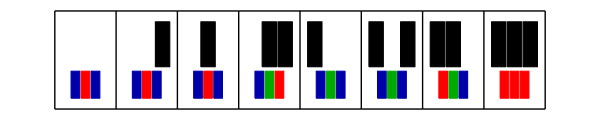

```mathematica
plot=createBZRule2Table[{30,7}]
```

```mathematica
Export[baseDirectory<>"Rule30-7_BZCA.svg",plot]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/Rule30-7_BZCA.svg

```mathematica
Export[baseDirectory<>"Rule30-7_BZCA.png",plot,ImageResolution->300]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/Rule30-7_BZCA.png

```mathematica
data= createBZRule2Table[{30,#}]&/@Range[0,15];
```

Rule Table: Cell Stirrers 
{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

Rule Table: Interfacial Stirrers 
{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

Rule Table: Cell Stirrers 
{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

Rule Table: Interfacial Stirrers 
{{1,1},{1,0},{0,0},{0,0},{0,1},{0,0},{0,0},{0,0}}

Rule Table: Cell Stirrers 
{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

Rule Table: Interfacial Stirrers 
{{0,0},{0,1},{1,0},{1,0},{0,0},{0,1},{0,0},{0,0}}

Rule Table: Cell Stirrers 
{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

Rule Table: Interfacial Stirrers 
{{1,1},{1,1},{1,0},{1,0},{0,1},{0,1},{0,0},{0,0}}

Rule Table: Cell Stirrers 
{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

Rule Table: Interfacial Stirrers 
{{0,0},{0,0},{0,1},{0,0},{1,0},{1,0},{0,1},{0,0}}

Rule Table: Cell Stirrers 
{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

Rule Table: Interfacial Stirrers 
{{1,1},{1,0},{0,1},{0,0},{1,1},{1,0},{0,1},{0,0}}

Rule Table: Cell Stirrers 
{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

Rule Table: Interfacial Stirrers 
{{0,0},{0,1},{1,1},{1,0},{1,0},{1,1},{0,1},{0,0}}

Rule Table: Cell Stirrers 
{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

Rule Table: Interfacial Stirrers 
{{1,1},{1,1},{1,1},{1,0},{1,1},{1,1},{0,1},{0,0}}

Rule Table: Cell Stirrers 
{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

Rule Table: Interfacial Stirrers 
{{0,0},{0,0},{0,0},{0,1},{0,0},{0,0},{1,0},{1,1}}

Rule Table: Cell Stirrers 
{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

Rule Table: Interfacial Stirrers 
{{1,1},{1,0},{0,0},{0,1},{0,1},{0,0},{1,0},{1,1}}

Rule Table: Cell Stirrers 
{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

Rule Table: Interfacial Stirrers 
{{0,0},{0,1},{1,0},{1,1},{0,0},{0,1},{1,0},{1,1}}

Rule Table: Cell Stirrers 
{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

Rule Table: Interfacial Stirrers 
{{1,1},{1,1},{1,0},{1,1},{0,1},{0,1},{1,0},{1,1}}

Rule Table: Cell Stirrers 
{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

Rule Table: Interfacial Stirrers 
{{0,0},{0,0},{0,1},{0,1},{1,0},{1,0},{1,1},{1,1}}

Rule Table: Cell Stirrers 
{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

Rule Table: Interfacial Stirrers 
{{1,1},{1,0},{0,1},{0,1},{1,1},{1,0},{1,1},{1,1}}

Rule Table: Cell Stirrers 
{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

Rule Table: Interfacial Stirrers 
{{0,0},{0,1},{1,1},{1,1},{1,0},{1,1},{1,1},{1,1}}

Rule Table: Cell Stirrers 
{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

Rule Table: Interfacial Stirrers 
{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}

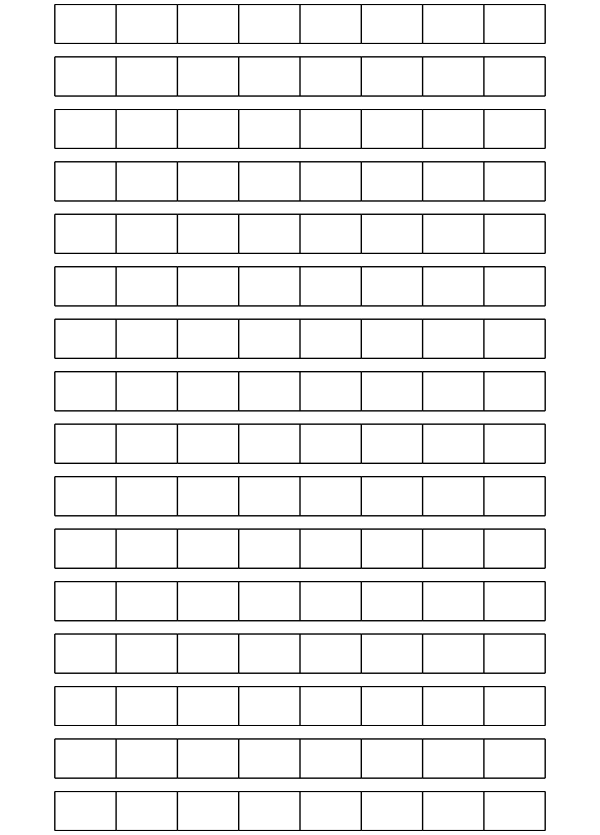

```mathematica
Rule30BZCA=GraphicsColumn[data,ImageSize->600]
```

```mathematica
Export[baseDirectory<>"Rule30_BZCA_All.png",Rule30BZCA,ImageResolution-> 300]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/Rule30_BZCA_All.png

```mathematica
Export[baseDirectory<>"Rule30_BZCA_All.svg",Rule30BZCA]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/Rule30_BZCA_All.svg

```mathematica
createBZRule2[{ruleC_,ruleI_}]:=Block[{str1,str2,chemStates,PWMCStates,PWMIStates,IntfRules,ruleMat,ruleMat2,ruleMatF},chemStates=Reverse[Tuples[{0,1},3]] ;str1=StringSplit[First@StringSplit@ToString@BaseForm[ruleC,2],""];PWMCStates=Flatten@{ConstantArray[0,8-Length[str1]],ToExpression/@str1};
str2=StringSplit[First@StringSplit@ToString@BaseForm[ruleI,2],""];
PWMIStates=Flatten@{ConstantArray[0,4-Length[str2]],ToExpression/@str2};
ruleMat=MapThread[Flatten@{#1,#2}&,{chemStates,PWMCStates}];
IntfRules=MapThread[Flatten@{#1,#2}&,{Tuples[{0,1},2],PWMIStates}];
ruleMat2=Table[Which[#=={0,0},PWMIStates⟦1⟧,#=={0,1},PWMIStates⟦2⟧,#=={1,0},PWMIStates⟦3⟧,#=={1,1},PWMIStates⟦4⟧]&/@{chemStates⟦i⟧⟦1;;2⟧,chemStates⟦i⟧⟦2;;3⟧},{i,Length@chemStates}];
ruleMatF=MapThread[Partition[Flatten@{#1,#2},3]&,{ruleMat,ruleMat2}]]
```

```mathematica
TableForm[Evaluate[#⟦1⟧->#⟦2⟧&/@createBZRule2[{12,12}]]]
```

{1,1,1}→{0,0,0}
{1,1,0}→{0,0,0}
{1,0,1}→{0,0,1}
{1,0,0}→{0,0,1}
{0,1,1}→{1,1,0}
{0,1,0}→{1,1,0}
{0,0,1}→{0,1,1}
{0,0,0}→{0,1,1}

```mathematica
updateStirrerState[{ruleC_,ruleI_},{cellL_,cellC_,cellR_}]:=Module[{rule=createBZRule2[{ruleC,ruleI}],pos},
pos=First@Flatten@Position[rule⟦All,1⟧,{cellL,cellC,cellR}];
rule⟦pos,2⟧]
```

```mathematica
SeedRandom[110]
```

RandomGeneratorState[…]

```mathematica
BZStateModel[{PWMStateCL_,PWMStateC_,PWMStateCR_},{PWMStateIL_,PWMStateIR_}]:=Module[{prob1,pC1=1,pC2=0,pC3=0,pC4=1.0,pR=0.5},
prob1=Which[PWMStateC==1,pC1,
PWMStateC==0 && PWMStateCL==0 && PWMStateCR==0,pC2,
PWMStateC==0 && PWMStateIL==0 && PWMStateIR==0,pC3,
PWMStateC==0 && PWMStateCL==1 && PWMStateCR==1 &&PWMStateIL==1 && PWMStateIR==1,pC4,
True,pR];
RandomChoice[{prob1,1-prob1}->{1,0}]]
```

Testing CA with fixed boundary values

```mathematica
BZCellularAutomata[{ruleC_,ruleI_},{initC_,boundC_}]:=Module[{currentState=Flatten@{boundC,initC,boundC},lenC,ruleTable,CellStirrers,IntfStirrers,ss,CellPairs,IntfPairs},
lenC=Length@currentState;
ss=Table[updateStirrerState[{ruleC,ruleI},currentState⟦i-1;;i+1⟧],{i,2,lenC-1}];
CellStirrers=Flatten@{boundC,ss⟦All,1⟧,boundC};
IntfStirrers=Flatten@{ss⟦All,2⟧,Last@ss⟦All,3⟧};
CellPairs=Table[CellStirrers⟦i-1;;i+1⟧,{i,2,lenC-1}];
IntfPairs=Table[IntfStirrers⟦i;;i+1⟧,{i,1,lenC-2}];
Table[BZStateModel[CellPairs⟦i⟧,IntfPairs⟦i⟧],{i,lenC-2}]]
```

```mathematica
initState=ConstantArray[0,101];initState⟦51⟧=1;totalSteps=100;
```

```mathematica
rule30=ParallelTable[ArrayPlot[NestList[BZCellularAutomata[{30,i},{#,0}]&,initState,totalSteps],PlotLabel-> "Rule: 30-"<>ToString[i],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ImageSize->100],{i,0,15}];
```

```mathematica
Rule30CA=GraphicsGrid[Partition[rule30,4],ImageSize->700,Spacings-> {0,10}]
```

-Graphics-

```mathematica
Export[baseDirectory<>"BZCA_Rule30_All.svg",Rule30CA,ImageResolution-> 300]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/BZCA_Rule30_All.svg

```mathematica
rule30data=Table[NestList[BZCellularAutomata[{30,i},{#,0}]&,initState,totalSteps],{i,0,15}];
```

```mathematica
Dimensions@rule30data
```

{16,101,101}

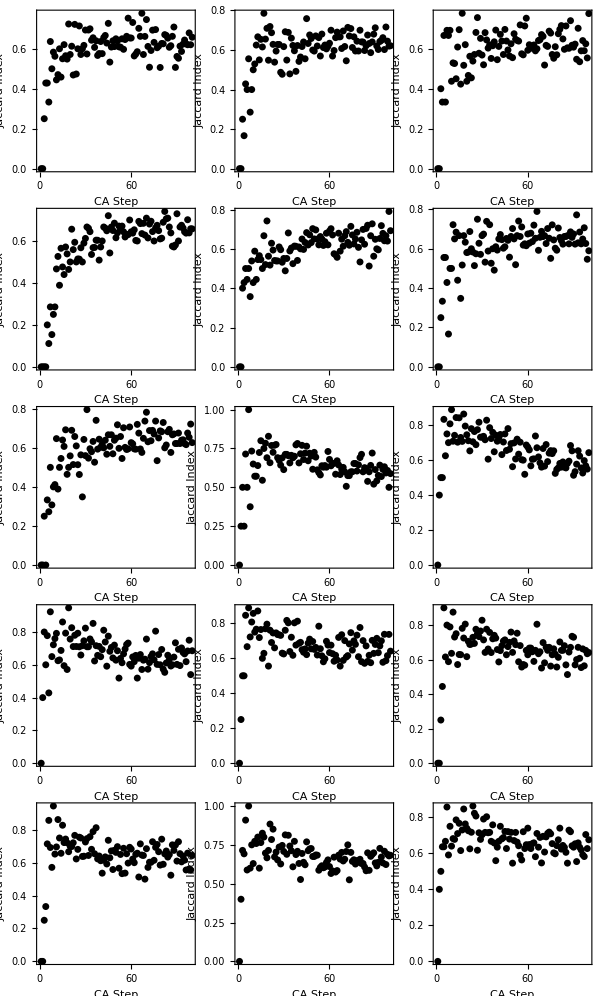

```mathematica
Rule30Jaccard=GraphicsGrid[Partition[Table[ListPlot[Table[JaccardDissimilarity[rule30data⟦1⟧⟦i⟧,rule30data⟦j⟧⟦i⟧],{i,totalSteps}],PlotRange-> Full,Frame-> True,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},FrameLabel->{"CA Step","Jaccard Index"},PlotStyle->{Black,PointSize[0.025]},AspectRatio->1,ImageSize->200],{j,2,16}],3],Spacings->{-5,-5},ImageSize->600]
```

```mathematica
Export[baseDirectory<>"BZCA_Rule30_All_Jaccard.svg",Rule30Jaccard]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/BZCA_Rule30_All_Jaccard.svg

```mathematica
Export[baseDirectory<>"BZCA_Rule30_All_Jaccard.png",Rule30Jaccard]
```

/Volumes/scapa4/group/0-Papers in Progress/0-submitted/BZ_CA_Computation_Abhishek_Marcus/Revision_5_NatComm/Final/Figures_Final_withData/Supp_Info/SI_Fig_49-52/BZ_StateSpace/BZCA_Rule30_All_Jaccard.png

```mathematica
initState=ConstantArray[0,100];initState⟦51⟧=1;totalSteps=100;
```

```mathematica
CAData=ParallelTable[NestList[BZCellularAutomata[{i,j},{#,0}]&,initState,totalSteps],{i,0,255},{j,0,15}];
(* This step will take some time ... *)
```

```mathematica
Dimensions@CAData
```

{256,16,101,100}

```mathematica
rulesList={30,101,102,105,109,110,126,131,133,145,149,250}+1; (* Setting some of the interesting elementary Cellular Automata rules *)
```

```mathematica
Table[Export[baseDirectory<>"BZCA_Rule"<>ToString[rulesList⟦i⟧-1]<>".svg",
GraphicsGrid[Partition[ArrayPlot[CAData⟦rulesList⟦i⟧,#⟧]&/@Range[16],4],ImageSize->600]],{i,Length@rulesList}];
```

```mathematica
Table[Export[baseDirectory<>"BZCA_Rule"<>ToString[rulesList⟦i⟧-1]<>".png",
GraphicsGrid[Partition[ArrayPlot[CAData⟦rulesList⟦i⟧,#⟧]&/@Range[16],4],ImageSize->600],ImageResolution-> 300],{i,Length@rulesList}];
```